```mathematica
data=Import["/home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p3.800_mu.100_0.nc","Data"]
```

Import::nffil: File /home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p3.800_mu.100_0.nc not found during Import.

$Failed

```mathematica
p0s
```

{}

```mathematica
p0s=Flatten[{Table[p,{p,3.83,3.85,0.001}],Table[p,{p,3.86,3.89,0.01}]}];
records={1,2,3,4,5,6,7,8};
```

```mathematica
timeEnergy=Table[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/gdRelaxation/data/N512/gdTimeEnergy_N512_p","_mu0.10_",".nc"},{p0s[[p]],records[[i]]},{3,0}],"Data"],{i,Length[records]}],{p,Length[p0s]}];
```

```mathematica
timeEnergy
```

{}

```mathematica
timeEnergyMean[[1,1]]
```

Part::partd: Part specification timeEnergyMean⟦1,1⟧ is longer than depth of object.

timeEnergyMean⟦1,1⟧

```mathematica
Table[Length[timeEnergy[[1,i,2]]],{i,Length[records]-1}]
```

{99,106,99,101,100,106,96,110}

```mathematica
Length[timeEnergyMean[[1]]]
```

110

```mathematica
time=Table[Table[Max[DeleteCases[Table[timeEnergy[[p,i,1,rec]],{i,Length[records]}],_Missing|_Part|0.]],{rec,Max[Table[Length[timeEnergy[[p,i,2]]],{i,Length[records]-1}]]}],{p,Length[p0s]}];
```

Part::partw: Part 111 of … does not exist.

Part::partw: Part 112 of … does not exist.

Part::partw: Part 113 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
timeEnergyMean=Table[Table[Total[DeleteCases[Table[timeEnergy[[p,i,2,rec]],{i,Length[records]}],_Missing|_Part|0.]]/9,{rec,Max[Table[Length[timeEnergy[[p,i,2]]],{i,Length[records]-1}]]}],{p,Length[p0s]}];
```

Part::partw: Part 111 of … does not exist.

Part::partw: Part 112 of … does not exist.

Part::partw: Part 113 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
timeEnergyMin=Table[Table[Min[DeleteCases[Table[timeEnergy[[p,i,2,rec]],{i,Length[records]}],_Missing|_Part|0.]],{rec,Min[Table[Length[timeEnergy[[p,i,2]]],{i,Length[records]-1}]]}],{p,Length[p0s]}];
```

Part::partw: Part 99 of … does not exist.

Part::partw: Part 100 of … does not exist.

Part::partw: Part 101 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

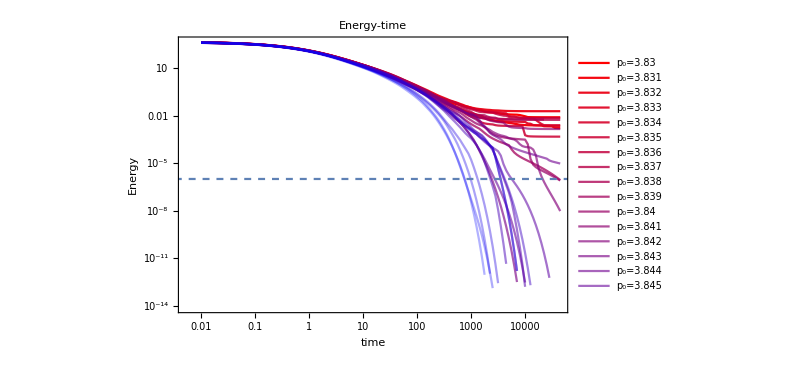

```mathematica
Show[ListLogLogPlot[Table[Table[{time[[p,rec]],timeEnergyMean[[p,rec]]},{rec,Max[Table[Length[timeEnergy[[p,i,2]]],{i,Length[records]-1}]]}],{p,Length[p0s]}],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"time","Energy"},ImageSize->600,PlotLabel->"Energy-time",Joined->True],LogLogPlot[10^-6,{x,0.001,100000},PlotStyle->Dashed]]
```

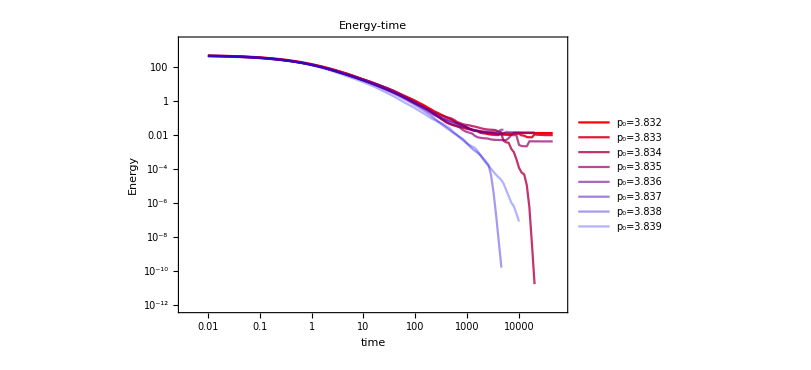

Part::partw: Part 111 of {411.964,395.556,380.402,368.824,359.161,350.263,342.126,333.888,326.527,320.092,«100»} does not exist.

Part::partw: Part 112 of {411.964,395.556,380.402,368.824,359.161,350.263,342.126,333.888,326.527,320.092,«100»} does not exist.

Part::partw: Part 113 of {411.964,395.556,380.402,368.824,359.161,350.263,342.126,333.888,326.527,320.092,«100»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

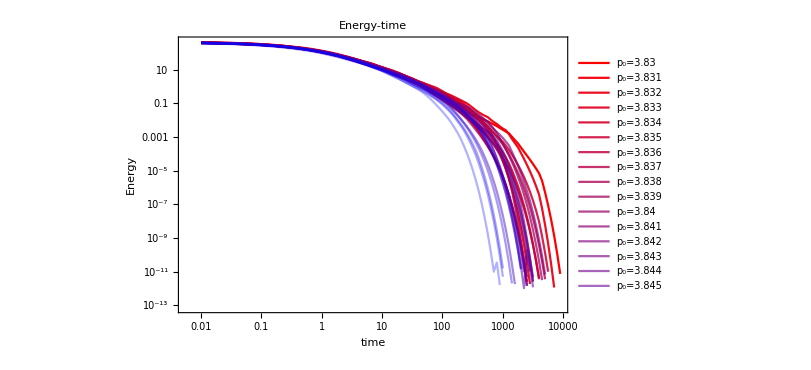

```mathematica
ListLogLogPlot[Table[Table[{time[[p,rec]],timeEnergyMin[[p,rec]]},{rec,Max[Table[Length[timeEnergy[[p,i,2]]],{i,Length[records]-1}]]}],{p,Length[p0s]}],PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,Length[p0s]}],PlotStyle->redBluePlotConfig[Length[p0s]],FrameLabel->{"time","Energy"},ImageSize->600,PlotLabel->"Energy-time",Joined->True]
```

```mathematica
Table[Show[ListLogLogPlot[Table[Table[{timeEnergy[[p,i,1,rec]],timeEnergy[[p,i,2,rec]]},{rec,Length[timeEnergy[[p,i,1]]]-1}],{i,Length[records]}],FrameLabel->{"time","Energy"},ImageSize->600,PlotLabel->"Energy-time p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->{{0.01,100000},{10^(-12),1200}}],LogLogPlot[10^-6,{x,0.001,100000},PlotStyle->Dashed]],{p,15,Length[p0s]}]
```

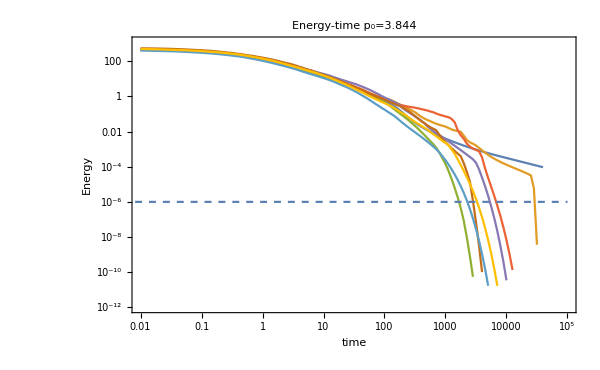
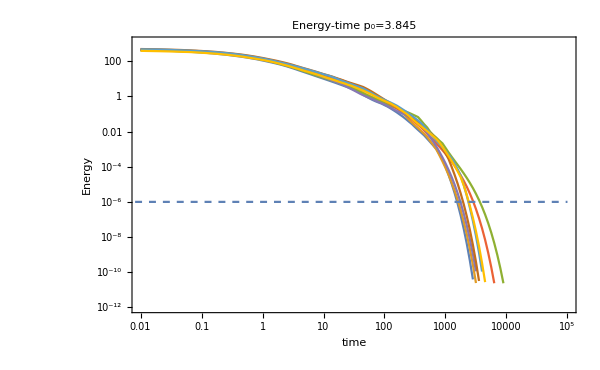
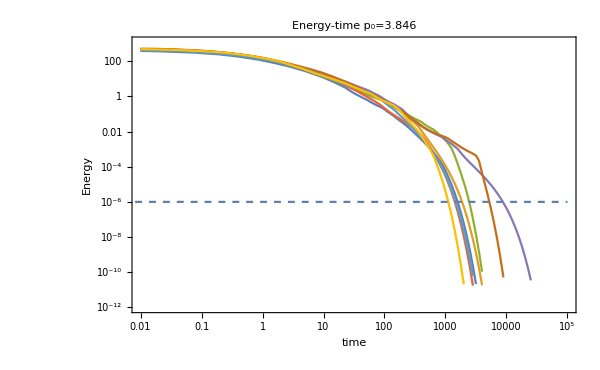
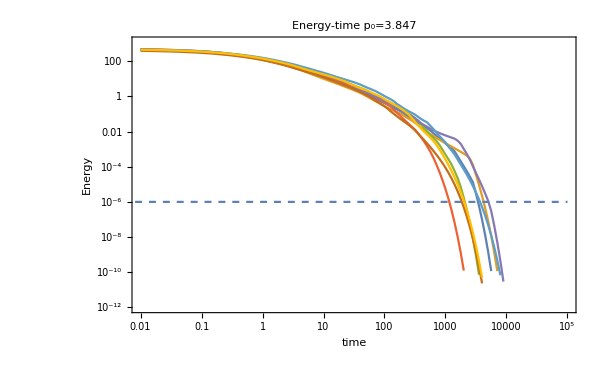
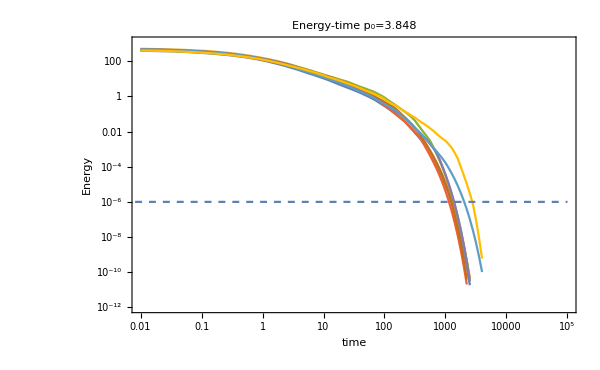
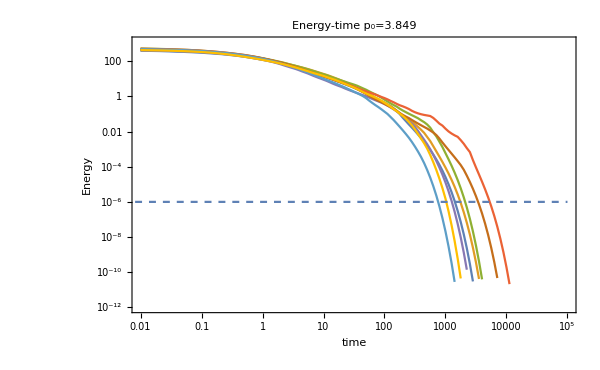
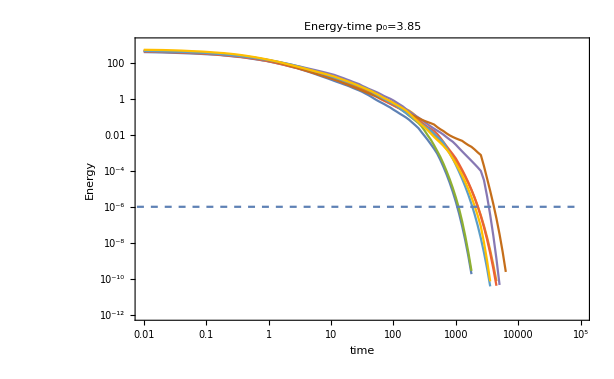
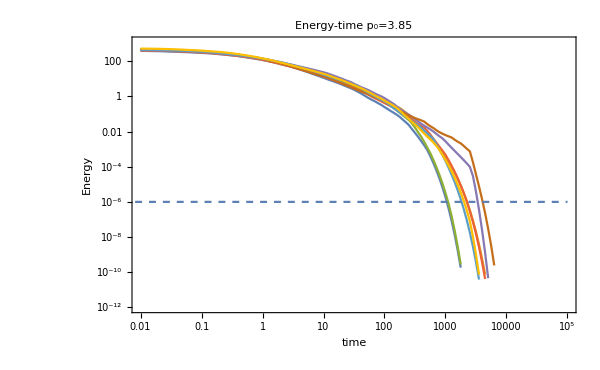

## find tau and fit them

```mathematica
tau={{1536.034702464721,1624.4719272494656,1750.358957821131,1957.7150873824974,2359.3195419846156,2403.756616349735,2896.861752601226,3692.1235894141532},{8775.541128871053,5302.409412825602,2513.7619554190105,1900.064016687115,1606.3296803828266,1490.8013353659546,1436.1913862712568,1126.8441577181095},{1135.2621460969822,1446.9203254210597,1501.9382332505138,1588.3563258275913,1878.8040445490064,2532.5407890163915,5442.44396371286,9007.617446726334},{1169.6914430304173,1864.9384613651996,2047.307815083688,2125.154943698746,3452.1330069281557,3719.65303364628,4238.65945019485,5108.175411792478},{1148.0679287009493,1260.335657915375,1308.258843347985,1383.5818690713918,1383.5818690713918,1308.258843347985,2047.307815083688,2708.563738585268},{770.1554483170962,1038.097237975875,1298.57631690174,1425.5620210274083,1783.3264426362366,2109.4265050572976,3426.5834994239694,5362.296011280625},{1045.8007441381055,1126.8441577181095,1830.4622550261763,2009.4602355873421,2289.8419665270817,3452.1330069281557,4083.391963297884,2332.9704516433303},{693.6924005380663,720.0694607564246,761.5274725183763,835.9960278509666,884.1285137352887,917.746744278788,988.866725188331,1606.3296803828266},{564.9707084730775,693.6924005380663,747.4494861293995,820.5413776563992,851.7417617363024,1045.8007441381055,1169.6914430304173,706.7578883792349},{513.2999859415241,532.7856046920355,542.804072052649,666.277467131755,704.574580520723,848.8243983633906,881.0470148949339,704.5498153864814},{386.11713755042035,465.3249668397131,492.1160599213515,501.3849179805695,627.2143680773322,755.8807331851823,814.4570491995376,894.0699660394222}};
```

```mathematica
Export["/home/chengling/Research/updates/04112024/meanTau.jpeg",ListPlot[Table[{p0s[[p]],Mean[tau[[p-15]]]},{p,16,Length[p0s]}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"p_0","τ"},ImageSize->600,PlotLabel->"Mean(τ) vs p_0"],ImageResolution->600]
```

/home/chengling/Research/updates/04112024/meanTau.jpeg

```mathematica
Export["/home/chengling/Research/updates/04112024/minTau.jpeg",ListPlot[Table[{p0s[[p]],Min[tau[[p-15]]]},{p,16,Length[p0s]}],Joined->True,PlotMarkers->Automatic,FrameLabel->{"p_0","τ"},ImageSize->600,PlotLabel->"Min(τ) vs p_0"],ImageResolution->600]
```

/home/chengling/Research/updates/04112024/minTau.jpeg